## SSS Paper plots

### Space Charge and Kinetic Energy

#### PES FWHM broadening

```mathematica
pes1067={{0.007,24/100 10},{0.04,24/100 10},{0.21,24/100 13},{0.84,24/100 19}};
pes1300={{0.1,24/100 10},{0.16,24/100 10},{0.19,24/100 12}};
pes1700={{0.95,24/100 15},{0.8,24/100 14},{0.65,24/100 13},{0.5,24/100 13},{0.41,24/100 12},{0.33,24/100 12},{0.25,24/100 12},{0.17,24/100 12}};
```

```mathematica
f1=FindFit[pes1067,m x+b,{m,b},x]
f2=FindFit[pes1300,m x+b,{m,b},x]
f3=FindFit[pes1700,m x+b,{m,b},x]
```

{m→2.60992,b→2.40423}

{m→4.57143,b→1.87429}

{m→0.939669,b→2.61312}

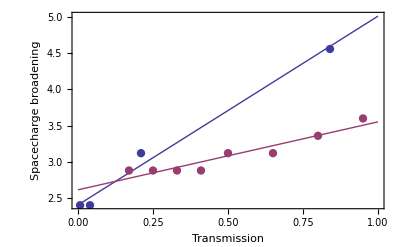

```mathematica
Show[Plot[{m x+b/.f1,m x+b/.f3},{x,0,1},Frame->True,FrameLabel->{"Transmission","Spacecharge broadening"},LabelStyle->Directive[16],PlotStyle->Thick,PlotRange->Full],ListPlot[{pes1067,pes1700},PlotStyle->PointSize[0.015]]]
```

#### Auger Voigt Profil broadening

```mathematica
auger04mm={{0.007,0.91},{0.04,0.87},{0.21,2.78}};
auger08mm={{0.007,1.22},{0.04,1.24},{0.21,3.11}};
auger13mm={{0.007,1.22},{0.04,1.23},{0.21,3.06}};
```

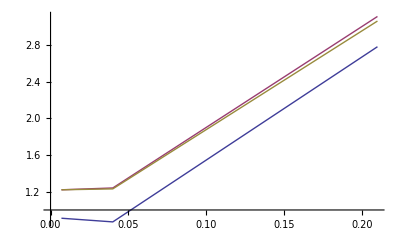

```mathematica
ListLinePlot[{auger04mm,auger08mm,auger13mm}]
```

#### Spacecharge effect vs electron count

```mathematica
spacechargedata135=Import["/Users/Max/owncloud/Doktor/amoi0214_data/spacecharge/run0135_schist"];
spacechargedata138=Import["/Users/Max/owncloud/Doktor/amoi0214_data/spacecharge/run0138_schist"];
spacechargedata077=Import["/Users/Max/owncloud/Doktor/amoi0214_data/spacecharge/run0077_schist"];
```

```mathematica
ListPlot3D[spacechargedata138,PlotRange->Full]
```

-Graphics3D-

```mathematica
{{0,100},{0,50},{0,10}}
```

```mathematica
ListPlot3D[spacechargedata077,PlotRange->Full]
```

-Graphics3D-

```mathematica
ListPlot3D[spacechargedata135,PlotRange->Full]
```

-Graphics3D-

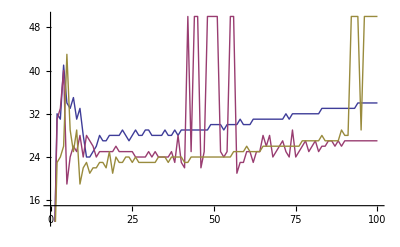

```mathematica
ListLinePlot[{Table[Ordering[ spacechargedata138[[All,x]],-1][[1]],{x,1,100}],Table[Ordering[ spacechargedata077[[All,x]],-1][[1]],{x,1,100}],Table[Ordering[ spacechargedata135[[All,x]],-1][[1]],{x,1,100}]}]
```

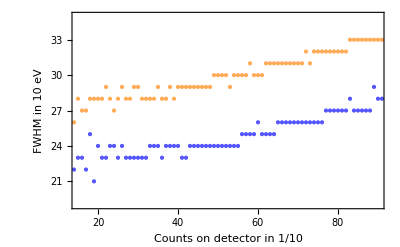

```mathematica
f=ListPlot[{Table[Ordering[ spacechargedata138[[All,x]],-1][[1]],{x,1,100}],Table[Ordering[ spacechargedata135[[All,x]],-1][[1]],{x,1,100}]},PlotRange->{{15,90},{19,35}},Frame->True,PlotStyle->{Directive[Thick,Lighter[Orange]],Directive[Thick,Lighter[Blue]]},FrameLabel->{"Counts on detector in 1/10","FWHM in 10 eV"}]
```

{m→0.0897656,b→28.2907}

{m→0.0912245,b→23.3316}

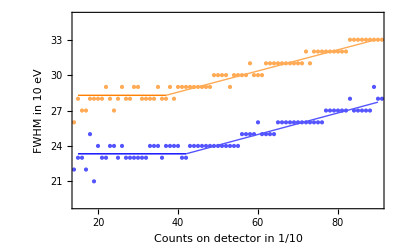

```mathematica
d3=37;
d4=42;
f12=FindFit[Table[Ordering[ spacechargedata138[[All,x]],-1][[1]],{x,d3,90}],m (x)+b,{m,b},x]
f22=FindFit[Table[Ordering[ spacechargedata135[[All,x]],-1][[1]],{x,d4,90}],m (x)+b,{m,b},x]
d1=Plot[{b/.f12},{x,15,d3},PlotStyle->{Directive[Thick,Orange]}];
d2=Plot[{b/.f22},{x,15,d4},PlotStyle->{Directive[Thick,Blue]}];
e1=Plot[{m (x-d3)+b/.f12},{x,d3,90},PlotStyle->{Directive[Thick,Lighter[Orange]]}];
e2=Plot[{m (x-d4)+b/.f22},{x,d4,90},PlotStyle->{Directive[Thick,Lighter[Blue]]}];
Show[{f,e1,e2,d1,d2}]
```

### Average Spectra and Single Shot data

#### Importiere daten

```mathematica
bcs082=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/run0082_BinnedCorrectedSpectra"]];
files1=FileNames["run0082*ShotSpectra",{"/Users/Max/ownCloud/Doktor/amoi0214_data/single-shot-data/"}];
files1//Length
pesSeededBS169=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/run0169_BinnedSpectra"]];
files2=FileNames["*",{"/Users/Max/ownCloud/Doktor/amoi0214_data/seeded-single-shot-data/"}];
files2//Length
bs165=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/run0165_BinnedSpectra"]];
files3=FileNames["run0165_c*",{"/Users/Max/ownCloud/Doktor/amoi0214_data/single-shot-data"}];
files3//Length
```

927

122

6088

#### Show single shot spectra from seeding

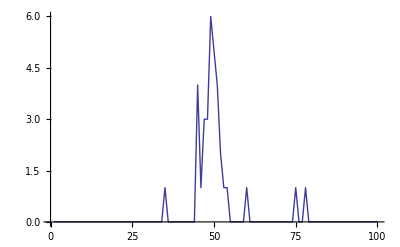

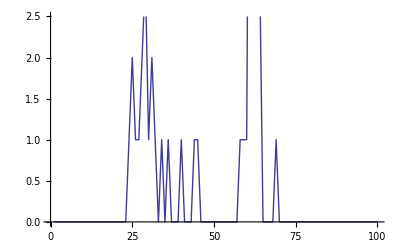

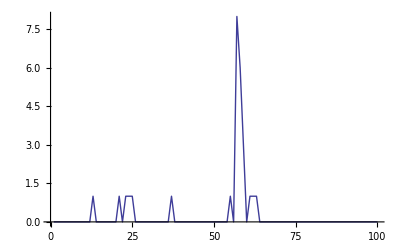

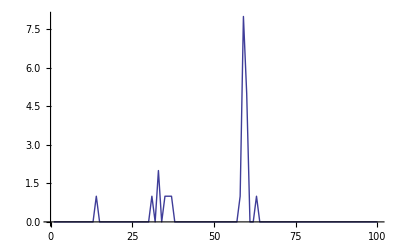

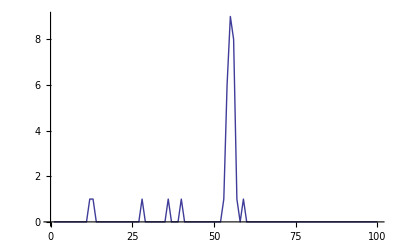

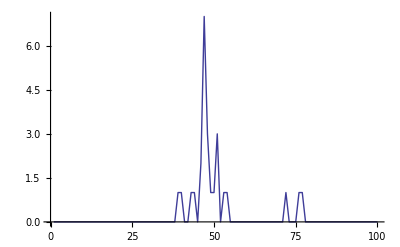

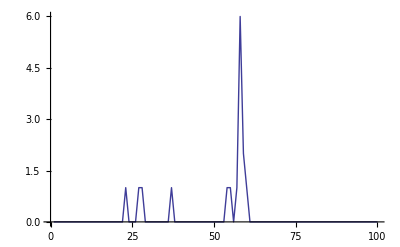

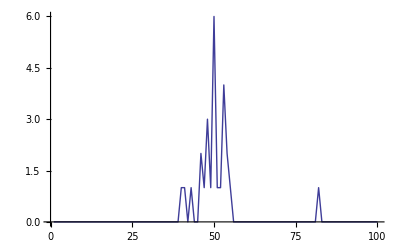

```mathematica
For[i=1,i<100,i++,singleShot=Flatten[Import[files3[[i]],"Table"]];
Print[ListLinePlot[singleShot]];]
```

#### Create plot

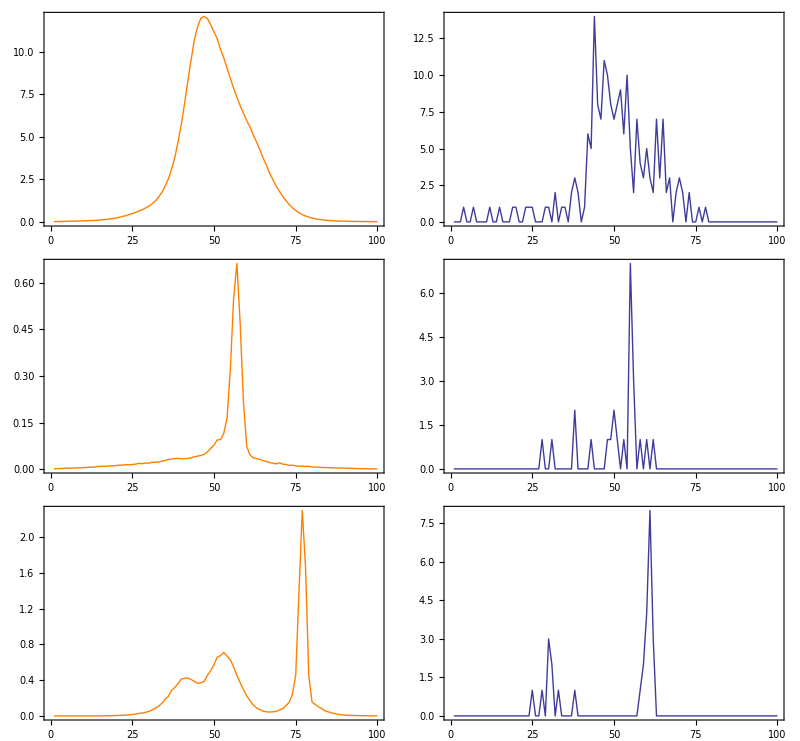

```mathematica
a=ListLinePlot[bcs082,PlotStyle->Directive[Thick,Orange],Frame->True,FrameTicks->{{True,True},{True,True}},FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]];

b1=ListLinePlot[Flatten[Import[files1[[2]],"Table"]],Frame->True,FrameTicks->{{True,True},{True,True}},PlotStyle->Directive[Thick,Blue],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]];
b2=ListLinePlot[Flatten[Import[files1[[15]],"Table"]],Frame->True,FrameTicks->{{True,True},{True,True}},PlotStyle->Directive[Thick,Blue],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]];
b3=ListLinePlot[Flatten[Import[files1[[1]],"Table"]],Frame->True,FrameTicks->{{True,True},{True,True}},PlotStyle->Directive[Thick,Blue],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]];

c=ListLinePlot[pesSeededBS169,PlotStyle->Directive[Thick,Orange],Frame->True,FrameTicks->{{True,True},{True,True}},PlotRange->Full,FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]];

d=ListLinePlot[Flatten[Import[files2[[2]],"Table"]],Frame->True,FrameTicks->{{True,True},{True,True}},PlotStyle->Thick,PlotRange->Full,FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]];

e=ListLinePlot[bs165,PlotStyle->Directive[Thick,Orange],Frame->True,PlotRange->Full,FrameTicks->{{True,True},{True,True}},FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]];

f=ListLinePlot[Flatten[Import[files3[[74]],"Table"]],Frame->True,FrameTicks->{{True,True},{True,True}},PlotStyle->Thick,PlotRange->Full,FrameTicksStyle->Directive[FontOpacity->0,FontSize->0]];


GraphicsGrid[{{a,b},{c,d},{e,f}},Spacings->Scaled[0]]
```

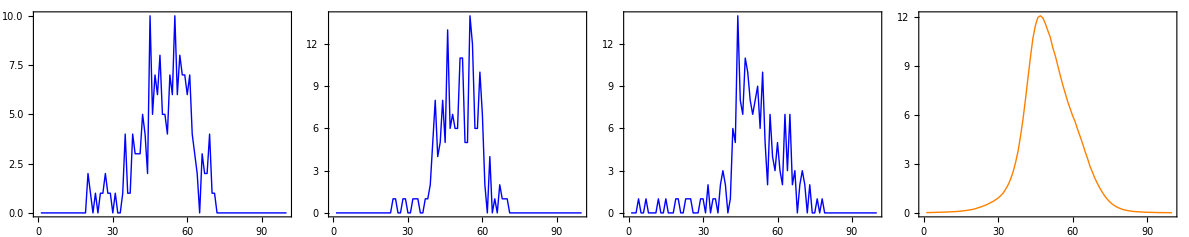

```mathematica
GraphicsRow[{b3,b2,b1,a},Spacings->Scaled[-0.035]]
```

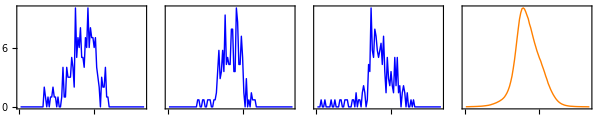

```mathematica
a=ListLinePlot[bcs082,PlotStyle->Directive[Thick,Orange],Frame->True,FrameTicks->{{None,True},{True,True}}];
b1=ListLinePlot[Flatten[Import[files1[[2]],"Table"]],Frame->True,FrameTicks->{{None,True},{True,True}},PlotStyle->Directive[Thick,Blue]];
b2=ListLinePlot[Flatten[Import[files1[[15]],"Table"]],Frame->True,FrameTicks->{{None,True},{True,True}},PlotStyle->Directive[Thick,Blue]];
b3=ListLinePlot[Flatten[Import[files1[[1]],"Table"]],Frame->True,FrameTicks->{{True,True},{True,True}},PlotStyle->Directive[Thick,Blue]];
GraphicsRow[{b3,b2,b1,a},Spacings->Scaled[-0.035]]
```

### Jitter plots

```mathematica
jitterdata169=Flatten[Import["/Users/Max/owncloud/Doktor/amoi0214_data/jitterdata/run0169_jitterhist"]];

jitterdata82=Flatten[Import["/Users/Max/owncloud/Doktor/amoi0214_data/jitterdata/run0082_jitterhist"]];
```

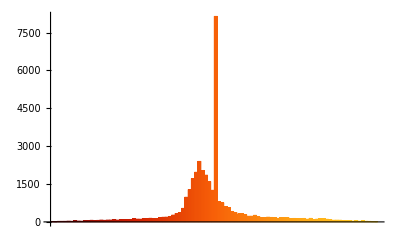

```mathematica
BarChart[jitterdata169,PlotRange->Automatic,ChartStyle-> "SolarColors",PlotRange->All]
```

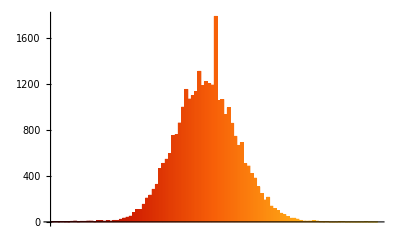

```mathematica
BarChart[jitterdata82,PlotRange->Automatic,ChartStyle-> "SolarColors"]
```

### Stability

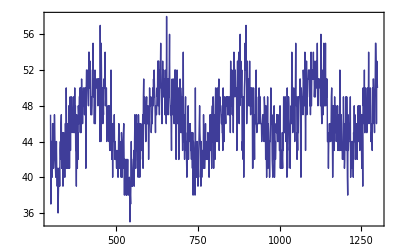

```mathematica
gasAttData=Delete[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/gas-attenuator-oscillations.csv","Table"],1];
ListLinePlot[gasAttData[[300;;1300]],Frame->True]
```

```mathematica
gasDet1=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/gasdet1.dat"]];
gasDet2=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/gasdet2.dat"]];
sss=Flatten[Import["/Users/Max/ownCloud/Doktor/amoi0214_data/sss.dat"]];
```

```mathematica
Length[gasDet1]==Length[sss]==Length[gasDet2]
gasDet1==gasDet2
```

True

False

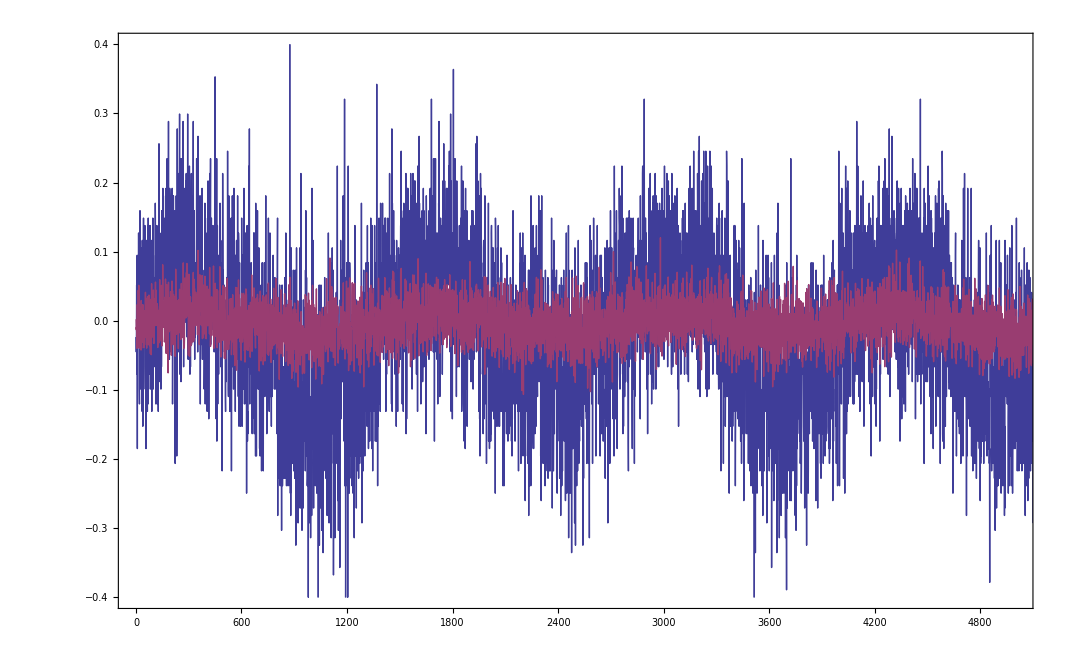

```mathematica
ListLinePlot[{-sss/Max[sss]+Mean[sss/Max[sss]],-gasDet1/Max[-gasDet1]-Mean[-gasDet1/Max[-gasDet1]](*,-gasDet2/Max[-gasDet2]-Mean[-gasDet2/Max[-gasDet2]]*)},PlotRange->{{0,5000},{-0.4,0.4}},Frame->True]
```

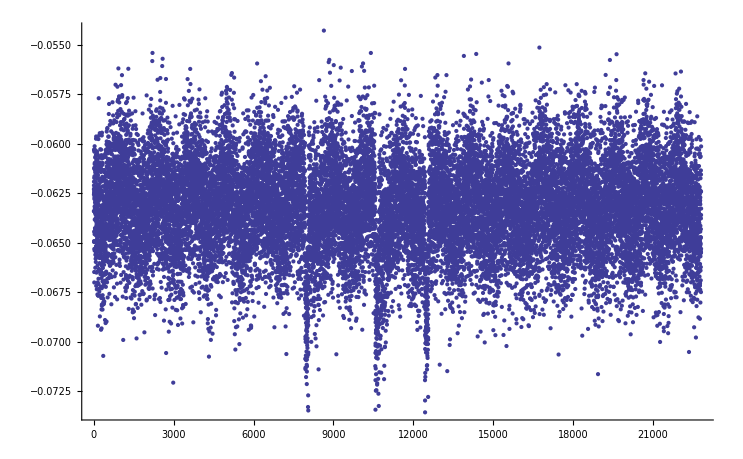

```mathematica
ListPlot[gasDet1]
```

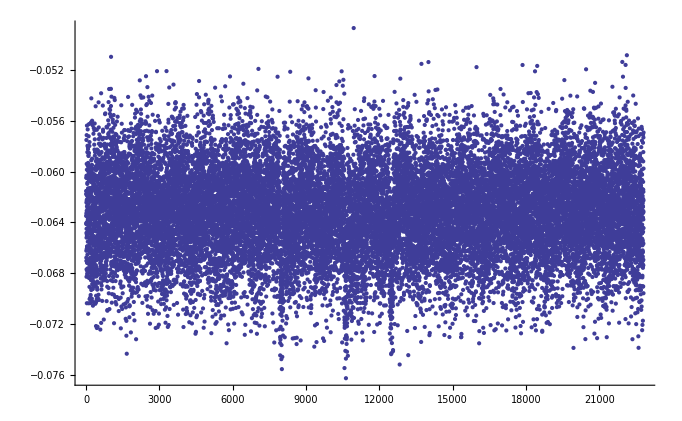

```mathematica
ListPlot[gasDet2]
```